## Initializing

```mathematica
resfinal={{12.900390625,13.8671875},{19.66796875,20.634765625},{28.369140625,29.3359375},{39.00390625,39.970703125},{50.60546875,51.572265625},{64.140625,65.107421875},{78.642578125,79.609375},{96.044921875,97.01171875},{113.447265625,114.4140625},{133.75,134.716796875},{155.01953125,155.986328125},{178.22265625,179.189453125},{202.392578125,203.359375},{228.49609375,229.462890625},{255.56640625,256.533203125},{285.537109375,286.50390625},{315.5078125,316.474609375},{348.37890625,349.345703125},{382.216796875,383.18359375},{417.98828125,418.955078125},{454.7265625,455.693359375},{493.3984375,494.365234375},{533.037109375,534.00390625},{574.609375,575.576171875},{618.115234375,619.08203125},{663.5546875,664.521484375},{709.9609375,710.927734375},{757.333984375,758.30078125},{807.607421875,808.57421875},{858.84765625,859.814453125},{911.0546875,912.021484375},{965.1953125,966.162109375}};
```

Above is from emcmanis_findcriticalvalues.nb. Run with rho_inf = 20*λ.

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=consts[[2]];
nn=consts[[3]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,ret},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]),
Return[Bisect[F,consts,x0,mid,ϵ]];,
Return[Bisect[F,consts,mid,xf,ϵ]];
];,
Return[mid];
]
]
```

```mathematica
rhoinfs={40*1000.,80*1000.,160*1000.};
```

### Junk?

```mathematica
ParallelTable[{i,j,Evaluate[$KernelID],Timing[Bisect[Critical,{0.01,rhoinfs[[j]],rhoinfs[[j]]/0.01},resfinal[[i,1]],resfinal[[i,2]],10.^(-6)]]},{i,1,2},{j,1,3}]
```

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 20.1514

```mathematica
Parallelize[Table[i,{i,1,10}]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
lcs=Parallelize[Table[Table[{j,Bisect[Critical,{0.01,rhoinfs[[j]],rhoinfs[[j]]/0.01},resfinal[[i,1]],resfinal[[i,2]],10^(-6)]},{j,1,3}],{i,1,Length[resfinal]}]];
```

```mathematica
ParallelTable[i+2,{i,1,10}]
```

{3,4,5,6,7,8,9,10,11,12}

## The Actual Computation

### Computing (TAKES A LONG TIME DO NOT EVALUATE)

{tag, rhoinf, lambda1, lambda2} = > {tag, lc[rhoinf]} <- format of this function below me

```mathematica
inputs=Table[Table[{j,rhoinfs[[j]],resfinal[[i,1]],resfinal[[i,2]]},{j,1,3}],{i,1,Length[resfinal]}]
```

{{{1,40000.,12.9004,13.8672},{2,80000.,12.9004,13.8672},{3,160000.,12.9004,13.8672}},{{1,40000.,19.668,20.6348},{2,80000.,19.668,20.6348},{3,160000.,19.668,20.6348}},{{1,40000.,28.3691,29.3359},{2,80000.,28.3691,29.3359},{3,160000.,28.3691,29.3359}},{{1,40000.,39.0039,39.9707},{2,80000.,39.0039,39.9707},{3,160000.,39.0039,39.9707}},{{1,40000.,50.6055,51.5723},{2,80000.,50.6055,51.5723},{3,160000.,50.6055,51.5723}},{{1,40000.,64.1406,65.1074},{2,80000.,64.1406,65.1074},{3,160000.,64.1406,65.1074}},{{1,40000.,78.6426,79.6094},{2,80000.,78.6426,79.6094},{3,160000.,78.6426,79.6094}},{{1,40000.,96.0449,97.0117},{2,80000.,96.0449,97.0117},{3,160000.,96.0449,97.0117}},{{1,40000.,113.447,114.414},{2,80000.,113.447,114.414},{3,160000.,113.447,114.414}},{{1,40000.,133.75,134.717},{2,80000.,133.75,134.717},{3,160000.,133.75,134.717}},{{1,40000.,155.02,155.986},{2,80000.,155.02,155.986},{3,160000.,155.02,155.986}},{{1,40000.,178.223,179.189},{2,80000.,178.223,179.189},{3,160000.,178.223,179.189}},{{1,40000.,202.393,203.359},{2,80000.,202.393,203.359},{3,160000.,202.393,203.359}},{{1,40000.,228.496,229.463},{2,80000.,228.496,229.463},{3,160000.,228.496,229.463}},{{1,40000.,255.566,256.533},{2,80000.,255.566,256.533},{3,160000.,255.566,256.533}},{{1,40000.,285.537,286.504},{2,80000.,285.537,286.504},{3,160000.,285.537,286.504}},{{1,40000.,315.508,316.475},{2,80000.,315.508,316.475},{3,160000.,315.508,316.475}},{{1,40000.,348.379,349.346},{2,80000.,348.379,349.346},{3,160000.,348.379,349.346}},{{1,40000.,382.217,383.184},{2,80000.,382.217,383.184},{3,160000.,382.217,383.184}},{{1,40000.,417.988,418.955},{2,80000.,417.988,418.955},{3,160000.,417.988,418.955}},{{1,40000.,454.727,455.693},{2,80000.,454.727,455.693},{3,160000.,454.727,455.693}},{{1,40000.,493.398,494.365},{2,80000.,493.398,494.365},{3,160000.,493.398,494.365}},{{1,40000.,533.037,534.004},{2,80000.,533.037,534.004},{3,160000.,533.037,534.004}},{{1,40000.,574.609,575.576},{2,80000.,574.609,575.576},{3,160000.,574.609,575.576}},{{1,40000.,618.115,619.082},{2,80000.,618.115,619.082},{3,160000.,618.115,619.082}},{{1,40000.,663.555,664.521},{2,80000.,663.555,664.521},{3,160000.,663.555,664.521}},{{1,40000.,709.961,710.928},{2,80000.,709.961,710.928},{3,160000.,709.961,710.928}},{{1,40000.,757.334,758.301},{2,80000.,757.334,758.301},{3,160000.,757.334,758.301}},{{1,40000.,807.607,808.574},{2,80000.,807.607,808.574},{3,160000.,807.607,808.574}},{{1,40000.,858.848,859.814},{2,80000.,858.848,859.814},{3,160000.,858.848,859.814}},{{1,40000.,911.055,912.021},{2,80000.,911.055,912.021},{3,160000.,911.055,912.021}},{{1,40000.,965.195,966.162},{2,80000.,965.195,966.162},{3,160000.,965.195,966.162}}}

```mathematica
inputs=Flatten[inputs,1]
```

{{1,40000.,12.9004,13.8672},{2,80000.,12.9004,13.8672},{3,160000.,12.9004,13.8672},{1,40000.,19.668,20.6348},{2,80000.,19.668,20.6348},{3,160000.,19.668,20.6348},{1,40000.,28.3691,29.3359},{2,80000.,28.3691,29.3359},{3,160000.,28.3691,29.3359},{1,40000.,39.0039,39.9707},{2,80000.,39.0039,39.9707},{3,160000.,39.0039,39.9707},{1,40000.,50.6055,51.5723},{2,80000.,50.6055,51.5723},{3,160000.,50.6055,51.5723},{1,40000.,64.1406,65.1074},{2,80000.,64.1406,65.1074},{3,160000.,64.1406,65.1074},{1,40000.,78.6426,79.6094},{2,80000.,78.6426,79.6094},{3,160000.,78.6426,79.6094},{1,40000.,96.0449,97.0117},{2,80000.,96.0449,97.0117},{3,160000.,96.0449,97.0117},{1,40000.,113.447,114.414},{2,80000.,113.447,114.414},{3,160000.,113.447,114.414},{1,40000.,133.75,134.717},{2,80000.,133.75,134.717},{3,160000.,133.75,134.717},{1,40000.,155.02,155.986},{2,80000.,155.02,155.986},{3,160000.,155.02,155.986},{1,40000.,178.223,179.189},{2,80000.,178.223,179.189},{3,160000.,178.223,179.189},{1,40000.,202.393,203.359},{2,80000.,202.393,203.359},{3,160000.,202.393,203.359},{1,40000.,228.496,229.463},{2,80000.,228.496,229.463},{3,160000.,228.496,229.463},{1,40000.,255.566,256.533},{2,80000.,255.566,256.533},{3,160000.,255.566,256.533},{1,40000.,285.537,286.504},{2,80000.,285.537,286.504},{3,160000.,285.537,286.504},{1,40000.,315.508,316.475},{2,80000.,315.508,316.475},{3,160000.,315.508,316.475},{1,40000.,348.379,349.346},{2,80000.,348.379,349.346},{3,160000.,348.379,349.346},{1,40000.,382.217,383.184},{2,80000.,382.217,383.184},{3,160000.,382.217,383.184},{1,40000.,417.988,418.955},{2,80000.,417.988,418.955},{3,160000.,417.988,418.955},{1,40000.,454.727,455.693},{2,80000.,454.727,455.693},{3,160000.,454.727,455.693},{1,40000.,493.398,494.365},{2,80000.,493.398,494.365},{3,160000.,493.398,494.365},{1,40000.,533.037,534.004},{2,80000.,533.037,534.004},{3,160000.,533.037,534.004},{1,40000.,574.609,575.576},{2,80000.,574.609,575.576},{3,160000.,574.609,575.576},{1,40000.,618.115,619.082},{2,80000.,618.115,619.082},{3,160000.,618.115,619.082},{1,40000.,663.555,664.521},{2,80000.,663.555,664.521},{3,160000.,663.555,664.521},{1,40000.,709.961,710.928},{2,80000.,709.961,710.928},{3,160000.,709.961,710.928},{1,40000.,757.334,758.301},{2,80000.,757.334,758.301},{3,160000.,757.334,758.301},{1,40000.,807.607,808.574},{2,80000.,807.607,808.574},{3,160000.,807.607,808.574},{1,40000.,858.848,859.814},{2,80000.,858.848,859.814},{3,160000.,858.848,859.814},{1,40000.,911.055,912.021},{2,80000.,911.055,912.021},{3,160000.,911.055,912.021},{1,40000.,965.195,966.162},{2,80000.,965.195,966.162},{3,160000.,965.195,966.162}}

```mathematica
inputs=Table[{inputs[[i,1]],inputs[[i,2]],inputs[[i,3]]-1,inputs[[i,4]]+1},{i,1,96}]
```

{{1,40000.,11.9004,14.8672},{2,80000.,11.9004,14.8672},{3,160000.,11.9004,14.8672},{1,40000.,18.668,21.6348},{2,80000.,18.668,21.6348},{3,160000.,18.668,21.6348},{1,40000.,27.3691,30.3359},{2,80000.,27.3691,30.3359},{3,160000.,27.3691,30.3359},{1,40000.,38.0039,40.9707},{2,80000.,38.0039,40.9707},{3,160000.,38.0039,40.9707},{1,40000.,49.6055,52.5723},{2,80000.,49.6055,52.5723},{3,160000.,49.6055,52.5723},{1,40000.,63.1406,66.1074},{2,80000.,63.1406,66.1074},{3,160000.,63.1406,66.1074},{1,40000.,77.6426,80.6094},{2,80000.,77.6426,80.6094},{3,160000.,77.6426,80.6094},{1,40000.,95.0449,98.0117},{2,80000.,95.0449,98.0117},{3,160000.,95.0449,98.0117},{1,40000.,112.447,115.414},{2,80000.,112.447,115.414},{3,160000.,112.447,115.414},{1,40000.,132.75,135.717},{2,80000.,132.75,135.717},{3,160000.,132.75,135.717},{1,40000.,154.02,156.986},{2,80000.,154.02,156.986},{3,160000.,154.02,156.986},{1,40000.,177.223,180.189},{2,80000.,177.223,180.189},{3,160000.,177.223,180.189},{1,40000.,201.393,204.359},{2,80000.,201.393,204.359},{3,160000.,201.393,204.359},{1,40000.,227.496,230.463},{2,80000.,227.496,230.463},{3,160000.,227.496,230.463},{1,40000.,254.566,257.533},{2,80000.,254.566,257.533},{3,160000.,254.566,257.533},{1,40000.,284.537,287.504},{2,80000.,284.537,287.504},{3,160000.,284.537,287.504},{1,40000.,314.508,317.475},{2,80000.,314.508,317.475},{3,160000.,314.508,317.475},{1,40000.,347.379,350.346},{2,80000.,347.379,350.346},{3,160000.,347.379,350.346},{1,40000.,381.217,384.184},{2,80000.,381.217,384.184},{3,160000.,381.217,384.184},{1,40000.,416.988,419.955},{2,80000.,416.988,419.955},{3,160000.,416.988,419.955},{1,40000.,453.727,456.693},{2,80000.,453.727,456.693},{3,160000.,453.727,456.693},{1,40000.,492.398,495.365},{2,80000.,492.398,495.365},{3,160000.,492.398,495.365},{1,40000.,532.037,535.004},{2,80000.,532.037,535.004},{3,160000.,532.037,535.004},{1,40000.,573.609,576.576},{2,80000.,573.609,576.576},{3,160000.,573.609,576.576},{1,40000.,617.115,620.082},{2,80000.,617.115,620.082},{3,160000.,617.115,620.082},{1,40000.,662.555,665.521},{2,80000.,662.555,665.521},{3,160000.,662.555,665.521},{1,40000.,708.961,711.928},{2,80000.,708.961,711.928},{3,160000.,708.961,711.928},{1,40000.,756.334,759.301},{2,80000.,756.334,759.301},{3,160000.,756.334,759.301},{1,40000.,806.607,809.574},{2,80000.,806.607,809.574},{3,160000.,806.607,809.574},{1,40000.,857.848,860.814},{2,80000.,857.848,860.814},{3,160000.,857.848,860.814},{1,40000.,910.055,913.021},{2,80000.,910.055,913.021},{3,160000.,910.055,913.021},{1,40000.,964.195,967.162},{2,80000.,964.195,967.162},{3,160000.,964.195,967.162}}

```mathematica
Length[inputs]
```

96

```mathematica
Findlc[input_,i_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[Ceiling[i,3]/3]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],10^(-6)]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs,inputs]
```

```mathematica
lcs=ParallelTable[Findlc[inputs[[i]],i],{i,1,96}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 2th lambda, part 2

***Beginning to calculate the 3th lambda, part 3

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 6th lambda, part 2

***Beginning to calculate the 7th lambda, part 3

***Beginning to calculate the 9th lambda, part 1

***Beginning to calculate the 10th lambda, part 2

Pass!

Bisecting. Midpoint is 113.931

Pass!

Bisecting. Midpoint is 51.0889

Pass!

Bisecting. Midpoint is 13.3838

Pass!

Bisecting. Midpoint is 134.233

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 12.6421

Pass!

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 12.8275

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 63.8823

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 113.351

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 113.363

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 63.6969

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 113.357

Bisecting. Midpoint is 50.4573

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 113.36

Bisecting. Midpoint is 50.4544

Bisecting. Midpoint is 63.7896

Bisecting. Midpoint is 12.6899

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 113.361

Bisecting. Midpoint is 50.4558

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 12.6906

Bisecting. Midpoint is 50.4551

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 63.836

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 132.993

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 50.4547

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 12.6904

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 132.988

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 132.99

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 63.8244

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 78.5697

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 63.8186

Bisecting. Midpoint is 132.988

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 63.8157

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 78.6624

Bisecting. Midpoint is 63.8142

***Beginning to calculate the 1th lambda, part 2

Bisecting. Midpoint is 50.4545

***Beginning to calculate the 9th lambda, part 2

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 19.774

***Beginning to calculate the 5th lambda, part 2

Bisecting. Midpoint is 28.4353

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 63.8135

Bisecting. Midpoint is 132.989

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 19.7736

Pass!

Bisecting. Midpoint is 51.0889

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 63.8139

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 78.7088

Bisecting. Midpoint is 19.7738

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 63.8137

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 78.7319

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 19.774

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 78.7435

Bisecting. Midpoint is 113.351

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 63.8136

***Beginning to calculate the 10th lambda, part 3

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 113.34

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 113.334

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 78.7493

Pass!

Bisecting. Midpoint is 134.233

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 28.4266

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 113.337

Bisecting. Midpoint is 50.4457

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 12.6899

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 50.4486

Bisecting. Midpoint is 12.6892

Bisecting. Midpoint is 78.7464

Bisecting. Midpoint is 113.337

Bisecting. Midpoint is 63.8136

***Beginning to calculate the 2th lambda, part 3

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 50.4471

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 28.4274

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6894

Bisecting. Midpoint is 50.4478

***Beginning to calculate the 6th lambda, part 3

Bisecting. Midpoint is 78.745

Bisecting. Midpoint is 113.338

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 50.4475

Bisecting. Midpoint is 12.6894

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 28.427

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 12.6895

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 78.7443

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 50.4478

Bisecting. Midpoint is 28.4268

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 63.8823

Bisecting. Midpoint is 78.7439

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 132.959

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 78.7437

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 132.97

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 78.7438

***Beginning to calculate the 9th lambda, part 3

Bisecting. Midpoint is 63.6969

***Beginning to calculate the 1th lambda, part 3

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 132.976

Bisecting. Midpoint is 50.4477

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 19.7342

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 78.7439

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 63.7896

Bisecting. Midpoint is 132.973

Bisecting. Midpoint is 50.4477

***Beginning to calculate the 5th lambda, part 3

Bisecting. Midpoint is 132.975

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.836

Pass!

Bisecting. Midpoint is 51.0889

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.8012

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.807

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.8099

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 132.974

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 113.305

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 19.7726

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 63.8084

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 38.5602

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 19.7729

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 113.316

Bisecting. Midpoint is 38.6992

Bisecting. Midpoint is 38.6761

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.8092

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 38.6645

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 38.6587

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 38.6558

Bisecting. Midpoint is 113.322

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 38.6572

Bisecting. Midpoint is 132.974

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 38.6565

Bisecting. Midpoint is 63.8088

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 38.6569

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 19.7732

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 113.325

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 63.8086

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 12.6899

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2535

Bisecting. Midpoint is 113.327

Bisecting. Midpoint is 50.4457

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2651

Bisecting. Midpoint is 12.6892

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2709

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2738

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2753

Bisecting. Midpoint is 113.326

***Beginning to calculate the 4th lambda, part 2

Bisecting. Midpoint is 95.276

Bisecting. Midpoint is 50.4428

Bisecting. Midpoint is 12.6888

Bisecting. Midpoint is 95.2763

Bisecting. Midpoint is 63.8088

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 19.7731

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 95.2765

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 95.2766

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 154.39

Bisecting. Midpoint is 12.689

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 50.4442

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 154.298

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 154.251

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 154.228

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 154.24

Bisecting. Midpoint is 38.5602

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 154.246

Bisecting. Midpoint is 50.445

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 154.248

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 154.249

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 38.6065

Bisecting. Midpoint is 12.6891

***Beginning to calculate the 8th lambda, part 2

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 50.4446

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 38.6297

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 154.25

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 38.6413

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 50.4444

Bisecting. Midpoint is 38.6471

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 38.65

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 113.326

***Beginning to calculate the 11th lambda, part 2

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 38.6514

Bisecting. Midpoint is 50.4443

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 38.6522

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 113.326

***Beginning to calculate the 3th lambda, part 1

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 38.6525

Bisecting. Midpoint is 154.39

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 95.2535

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 38.6527

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 154.298

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 95.2651

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 154.251

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 28.4353

Bisecting. Midpoint is 95.2593

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 154.228

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 95.2564

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 154.217

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.4324

Bisecting. Midpoint is 154.211

Bisecting. Midpoint is 95.2579

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 28.431

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.4303

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 154.214

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 28.4306

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.4308

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 95.259

Bisecting. Midpoint is 28.4309

Bisecting. Midpoint is 78.9406

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 154.211

Bisecting. Midpoint is 28.4309

Bisecting. Midpoint is 78.8478

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 95.2588

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 78.8015

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 78.7783

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 78.7667

Bisecting. Midpoint is 95.2587

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 78.7609

Bisecting. Midpoint is 28.431

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 78.7638

Bisecting. Midpoint is 113.326

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 78.7653

***Beginning to calculate the 4th lambda, part 3

***Beginning to calculate the 3th lambda, part 2

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 78.7645

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 78.7642

Bisecting. Midpoint is 50.4443

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 78.764

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 78.7639

Pass!

Bisecting. Midpoint is 39.4873

Pass!

Bisecting. Midpoint is 134.233

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 19.7754

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 19.7758

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 133.017

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 19.7756

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 133.022

***Beginning to calculate the 11th lambda, part 3

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 19.7755

***Beginning to calculate the 7th lambda, part 2

Bisecting. Midpoint is 28.4353

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 133.018

Bisecting. Midpoint is 19.7755

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 133.019

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 19.7755

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 38.5602

***Beginning to calculate the 8th lambda, part 3

Bisecting. Midpoint is 133.019

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 63.8823

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 63.6969

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 63.7896

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 28.4266

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 78.5697

Bisecting. Midpoint is 63.836

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 154.39

Pass!

Bisecting. Midpoint is 202.876

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 78.6624

Bisecting. Midpoint is 63.8244

Bisecting. Midpoint is 202.134

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 201.763

Bisecting. Midpoint is 63.8186

Bisecting. Midpoint is 28.4288

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 38.6065

Bisecting. Midpoint is 201.578

Bisecting. Midpoint is 63.8215

Bisecting. Midpoint is 78.7088

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 201.485

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 63.8229

Bisecting. Midpoint is 28.4285

Bisecting. Midpoint is 201.439

***Beginning to calculate the 14th lambda, part 2

Bisecting. Midpoint is 63.8237

Bisecting. Midpoint is 201.416

Bisecting. Midpoint is 78.7319

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 28.4283

Bisecting. Midpoint is 201.427

Fail!

***Beginning to calculate the 14th lambda, part 3

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 38.6297

Bisecting. Midpoint is 63.8235

Bisecting. Midpoint is 201.433

Bisecting. Midpoint is 154.112

Bisecting. Midpoint is 78.7435

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 28.4282

Bisecting. Midpoint is 63.8234

Bisecting. Midpoint is 201.429

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 78.7493

Bisecting. Midpoint is 63.8234

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 154.159

Fail!

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 38.6413

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 78.7522

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 78.7508

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 154.182

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 38.6471

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.845

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 78.7501

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.891

***Beginning to calculate the 15th lambda, part 3

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.914

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 78.7504

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.902

Bisecting. Midpoint is 38.65

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 254.908

Bisecting. Midpoint is 78.7506

***Beginning to calculate the 13th lambda, part 2

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 254.905

Bisecting. Midpoint is 154.188

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 254.904

Fail!

***Beginning to calculate the 13th lambda, part 3

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 254.903

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 38.6514

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 154.19

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 95.2535

***Beginning to calculate the 17th lambda, part 1

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 254.904

Pass!

Bisecting. Midpoint is 315.991

Fail!

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 315.25

Fail!

***Beginning to calculate the 18th lambda, part 2

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 314.879

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 38.6507

Bisecting. Midpoint is 154.192

Bisecting. Midpoint is 314.693

Fail!

***Beginning to calculate the 18th lambda, part 3

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 95.2419

Bisecting. Midpoint is 314.601

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 314.647

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 314.67

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 38.6504

Fail!

***Beginning to calculate the 19th lambda, part 1

Bisecting. Midpoint is 314.682

Bisecting. Midpoint is 254.904

Fail!

***Beginning to calculate the 19th lambda, part 2

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 314.676

Bisecting. Midpoint is 95.2477

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 314.673

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 19th lambda, part 3

Bisecting. Midpoint is 314.674

***Beginning to calculate the 15th lambda, part 2

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 254.845

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 95.2506

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 314.674

Fail!

***Beginning to calculate the 20th lambda, part 1

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 314.674

Fail!

***Beginning to calculate the 20th lambda, part 2

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 254.798

Bisecting. Midpoint is 314.674

Fail!

***Beginning to calculate the 20th lambda, part 3

Bisecting. Midpoint is 154.193

***Beginning to calculate the 21th lambda, part 1

Bisecting. Midpoint is 95.2492

Bisecting. Midpoint is 314.674

Fail!

***Beginning to calculate the 21th lambda, part 2

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 21th lambda, part 3

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 254.845

Fail!

***Beginning to calculate the 22th lambda, part 2

Bisecting. Midpoint is 254.775

***Beginning to calculate the 17th lambda, part 2

Bisecting. Midpoint is 95.2499

Fail!

***Beginning to calculate the 22th lambda, part 3

Bisecting. Midpoint is 254.798

Pass!

Bisecting. Midpoint is 315.991

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 315.25

Fail!

***Beginning to calculate the 22th lambda, part 1

Bisecting. Midpoint is 254.821

Bisecting. Midpoint is 254.787

Fail!

***Beginning to calculate the 23th lambda, part 3

Fail!

***Beginning to calculate the 23th lambda, part 1

Bisecting. Midpoint is 314.879

Bisecting. Midpoint is 95.2495

Bisecting. Midpoint is 254.81

Fail!

***Beginning to calculate the 23th lambda, part 2

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 314.693

Bisecting. Midpoint is 38.6504

Fail!

***Beginning to calculate the 25th lambda, part 1

Bisecting. Midpoint is 254.781

Bisecting. Midpoint is 254.816

Bisecting. Midpoint is 314.601

Fail!

***Beginning to calculate the 25th lambda, part 2

Fail!

***Beginning to calculate the 24th lambda, part 1

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 24th lambda, part 2

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 254.818

Fail!

***Beginning to calculate the 25th lambda, part 3

Bisecting. Midpoint is 314.554

Fail!

***Beginning to calculate the 24th lambda, part 3

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.577

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 26th lambda, part 1

Bisecting. Midpoint is 95.2496

Bisecting. Midpoint is 314.566

Bisecting. Midpoint is 254.821

Fail!

***Beginning to calculate the 26th lambda, part 2

Fail!

***Beginning to calculate the 27th lambda, part 3

Bisecting. Midpoint is 314.56

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 254.779

Fail!

***Beginning to calculate the 26th lambda, part 3

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.557

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 314.559

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 28th lambda, part 1

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 27th lambda, part 1

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 38.6504

Fail!

***Beginning to calculate the 28th lambda, part 2

Fail!

***Beginning to calculate the 27th lambda, part 2

Bisecting. Midpoint is 314.557

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 95.2497

Fail!

***Beginning to calculate the 29th lambda, part 1

Fail!

***Beginning to calculate the 28th lambda, part 3

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 29th lambda, part 2

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 29th lambda, part 3

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 30th lambda, part 2

Fail!

***Beginning to calculate the 12th lambda, part 2

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.78

Fail!

***Beginning to calculate the 12th lambda, part 3

Bisecting. Midpoint is 38.6504

Fail!

***Beginning to calculate the 30th lambda, part 3

Fail!

***Beginning to calculate the 30th lambda, part 1

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 31th lambda, part 3

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 95.2497

Fail!

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.78

Fail!

***Beginning to calculate the 31th lambda, part 1

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 32th lambda, part 1

Fail!

***Beginning to calculate the 31th lambda, part 2

Fail!

***Beginning to calculate the 32th lambda, part 2

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 32th lambda, part 3

Bisecting. Midpoint is 314.558

Fail!

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 314.558

Fail!

Bisecting. Midpoint is 254.78

***Beginning to calculate the 17th lambda, part 3

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 254.78

Fail!

***Beginning to calculate the 18th lambda, part 1

Bisecting. Midpoint is 95.2497

Fail!

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 254.78

«1 more identical outputs»

***Beginning to calculate the 16th lambda, part 1

Fail!

***Beginning to calculate the 16th lambda, part 2

Fail!

***Beginning to calculate the 16th lambda, part 3

Fail!

{{1,12.6903},{2,12.6895},{3,12.6891},{1,19.7755},{2,19.7739},{3,19.7731},{1,28.431},{2,28.4281},{3,28.4267},{1,38.6571},{2,38.6526},{3,38.6504},{1,50.4545},{2,50.4477},{3,50.4443},{1,63.8233},{2,63.8136},{3,63.8087},{1,78.764},{2,78.7505},{3,78.7438},{1,95.2767},{2,95.2586},{3,95.2497},{1,113.362},{2,113.338},{3,113.326},{1,133.019},{2,132.989},{3,132.974},{1,154.25},{2,154.212},{3,154.193},{1,Null},{2,Null},{3,Null},{1,201.43},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,254.904},{2,254.82},{3,254.78},{1,Null},{2,Null},{3,Null},{1,314.674},{2,314.558},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null}}

### Data (evaluate me!)

```mathematica
lcs={{1,12.690344190457836},{2,12.689524383982643},{3,12.6891141270753},{1,19.775537554407492},{2,19.773917039623484},{3,19.77310855058022},{1,28.4309580035042},{2,28.428132182219997},{3,28.42672174726613},{1,38.65714240842499},{2,38.652617557672784},{3,38.65036114468239},{1,50.45449365139939},{2,50.44768833811395},{3,50.444298767251894},{1,63.82334306859411},{2,63.81358461291529},{3,63.80873155663721},{1,78.76398036791943},{2,78.75050342851318},{3,78.74381058220752},{1,95.27667281893082},{2,95.25861514895223},{3,95.2496616456192},{1,113.36167274531908},{2,113.3380695336964},{3,113.32638923660852},{1,133.0192236683797},{2,132.98900753981434},{3,132.97408621315844},{1,154.24956618831493},{2,154.2115601298865},{3,154.19283614610322},{1,Null},{2,Null},{3,Null},{1,201.42959072510712},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,254.90370993013494},{2,254.8203860449139},{3,254.77981941751204},{1,Null},{2,Null},{3,Null},{1,314.6739881213289},{2,314.5576463358011},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null}};
```

```mathematica
leftovers={};
```

```mathematica
For[i=1,i≤Length[lcs],i++,
If[lcs[[i,2]]==Null,
leftovers=Append[leftovers,i]
]
]
```

### Expanding Ranges (In-progress, do NOT evaluate)

This bit expands my ranges I'm searching in.

```mathematica
leftovers
```

{34,35,36,38,39,40,41,42,46,47,48,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96}

```mathematica
newins={};
```

```mathematica
For[i=1,i≤Length[leftovers],i++,
item=leftovers[[i]];
newins=Append[newins,{inputs[[item,1]],inputs[[item,2]],inputs[[item,3]]-1,inputs[[item,4]]+1,item}]
]
```

```mathematica
newins
```

{{1,40000.,176.223,181.189,34},{2,80000.,176.223,181.189,35},{3,160000.,176.223,181.189,36},{2,80000.,200.393,205.359,38},{3,160000.,200.393,205.359,39},{1,40000.,226.496,231.463,40},{2,80000.,226.496,231.463,41},{3,160000.,226.496,231.463,42},{1,40000.,283.537,288.504,46},{2,80000.,283.537,288.504,47},{3,160000.,283.537,288.504,48},{3,160000.,313.508,318.475,51},{1,40000.,346.379,351.346,52},{2,80000.,346.379,351.346,53},{3,160000.,346.379,351.346,54},{1,40000.,380.217,385.184,55},{2,80000.,380.217,385.184,56},{3,160000.,380.217,385.184,57},{1,40000.,415.988,420.955,58},{2,80000.,415.988,420.955,59},{3,160000.,415.988,420.955,60},{1,40000.,452.727,457.693,61},{2,80000.,452.727,457.693,62},{3,160000.,452.727,457.693,63},{1,40000.,491.398,496.365,64},{2,80000.,491.398,496.365,65},{3,160000.,491.398,496.365,66},{1,40000.,531.037,536.004,67},{2,80000.,531.037,536.004,68},{3,160000.,531.037,536.004,69},{1,40000.,572.609,577.576,70},{2,80000.,572.609,577.576,71},{3,160000.,572.609,577.576,72},{1,40000.,616.115,621.082,73},{2,80000.,616.115,621.082,74},{3,160000.,616.115,621.082,75},{1,40000.,661.555,666.521,76},{2,80000.,661.555,666.521,77},{3,160000.,661.555,666.521,78},{1,40000.,707.961,712.928,79},{2,80000.,707.961,712.928,80},{3,160000.,707.961,712.928,81},{1,40000.,755.334,760.301,82},{2,80000.,755.334,760.301,83},{3,160000.,755.334,760.301,84},{1,40000.,805.607,810.574,85},{2,80000.,805.607,810.574,86},{3,160000.,805.607,810.574,87},{1,40000.,856.848,861.814,88},{2,80000.,856.848,861.814,89},{3,160000.,856.848,861.814,90},{1,40000.,909.055,914.021,91},{2,80000.,909.055,914.021,92},{3,160000.,909.055,914.021,93},{1,40000.,963.195,968.162,94},{2,80000.,963.195,968.162,95},{3,160000.,963.195,968.162,96}}

```mathematica
Length[newins]
```

57

```mathematica
DistributeDefinitions[newins]
```

Only looking at first thru thirtieth here, just because. Could I guess do timing, don't actually give much of a shit.

```mathematica
addtllcs=ParallelTable[Findlc[newins[[i]],newins[[i,5]]],{i,1,30}]
```

***Beginning to calculate the 12th lambda, part 1

***Beginning to calculate the 12th lambda, part 3

***Beginning to calculate the 13th lambda, part 3

***Beginning to calculate the 14th lambda, part 2

***Beginning to calculate the 16th lambda, part 1

***Beginning to calculate the 16th lambda, part 3

***Beginning to calculate the 18th lambda, part 1

***Beginning to calculate the 18th lambda, part 3

Pass!

Bisecting. Midpoint is 178.706

Pass!

Bisecting. Midpoint is 348.862

Pass!

Bisecting. Midpoint is 286.021

Bisecting. Midpoint is 177.464

Bisecting. Midpoint is 284.779

Pass!

Bisecting. Midpoint is 228.979

Bisecting. Midpoint is 347.621

Bisecting. Midpoint is 176.844

Bisecting. Midpoint is 284.158

Bisecting. Midpoint is 177.154

Bisecting. Midpoint is 347.

Pass!

Bisecting. Midpoint is 348.862

Bisecting. Midpoint is 176.999

Bisecting. Midpoint is 283.848

Pass!

Bisecting. Midpoint is 178.706

Pass!

Bisecting. Midpoint is 202.876

Pass!

Bisecting. Midpoint is 286.021

Bisecting. Midpoint is 227.738

Bisecting. Midpoint is 346.689

Bisecting. Midpoint is 177.076

Bisecting. Midpoint is 284.003

Bisecting. Midpoint is 346.845

Bisecting. Midpoint is 177.038

Bisecting. Midpoint is 283.925

Bisecting. Midpoint is 227.117

Bisecting. Midpoint is 347.621

Bisecting. Midpoint is 346.922

Bisecting. Midpoint is 177.057

Bisecting. Midpoint is 283.964

Bisecting. Midpoint is 201.634

Bisecting. Midpoint is 346.883

Bisecting. Midpoint is 177.047

Bisecting. Midpoint is 177.464

Bisecting. Midpoint is 283.983

Bisecting. Midpoint is 346.903

Bisecting. Midpoint is 284.779

Bisecting. Midpoint is 227.427

Bisecting. Midpoint is 177.052

Bisecting. Midpoint is 283.993

Bisecting. Midpoint is 177.054

Bisecting. Midpoint is 346.912

Bisecting. Midpoint is 347.

Bisecting. Midpoint is 283.998

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.917

Bisecting. Midpoint is 227.272

Bisecting. Midpoint is 201.013

Bisecting. Midpoint is 284.

Bisecting. Midpoint is 346.92

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 176.844

Bisecting. Midpoint is 284.158

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 227.35

Bisecting. Midpoint is 346.689

Bisecting. Midpoint is 346.92

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 201.324

Bisecting. Midpoint is 227.311

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 346.845

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 283.848

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 177.154

Bisecting. Midpoint is 227.292

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 201.479

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 227.301

Bisecting. Midpoint is 346.767

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 176.999

Bisecting. Midpoint is 284.003

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 227.306

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 201.401

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.728

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 227.309

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 177.053

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

***Beginning to calculate the 12th lambda, part 2

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 283.925

Bisecting. Midpoint is 346.921

Bisecting. Midpoint is 284.002

Bisecting. Midpoint is 346.709

Bisecting. Midpoint is 176.921

Pass!

Bisecting. Midpoint is 178.706

***Beginning to calculate the 18th lambda, part 2

***Beginning to calculate the 16th lambda, part 2

Bisecting. Midpoint is 201.363

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.464

Pass!

Bisecting. Midpoint is 348.862

Bisecting. Midpoint is 346.718

Pass!

Bisecting. Midpoint is 286.021

Bisecting. Midpoint is 283.886

Bisecting. Midpoint is 176.844

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 176.96

Bisecting. Midpoint is 201.343

Bisecting. Midpoint is 347.621

Bisecting. Midpoint is 177.154

Bisecting. Midpoint is 284.779

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 346.723

Bisecting. Midpoint is 347.

Bisecting. Midpoint is 176.999

Bisecting. Midpoint is 283.867

Bisecting. Midpoint is 284.158

Bisecting. Midpoint is 176.979

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 201.353

Bisecting. Midpoint is 346.689

Bisecting. Midpoint is 177.076

Bisecting. Midpoint is 346.721

Bisecting. Midpoint is 283.848

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 346.845

Bisecting. Midpoint is 177.038

Bisecting. Midpoint is 176.989

Bisecting. Midpoint is 283.857

Bisecting. Midpoint is 201.348

Bisecting. Midpoint is 284.003

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.018

Bisecting. Midpoint is 346.72

Bisecting. Midpoint is 346.767

Bisecting. Midpoint is 283.925

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.008

Bisecting. Midpoint is 176.984

Bisecting. Midpoint is 346.806

Bisecting. Midpoint is 283.852

Bisecting. Midpoint is 201.346

Bisecting. Midpoint is 283.886

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.004

Bisecting. Midpoint is 346.786

Bisecting. Midpoint is 283.906

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 176.982

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 201.344

Bisecting. Midpoint is 346.777

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 283.896

Bisecting. Midpoint is 177.005

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 177.005

Bisecting. Midpoint is 346.781

Bisecting. Midpoint is 283.901

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 201.344

Bisecting. Midpoint is 283.856

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 346.784

Bisecting. Midpoint is 176.982

Bisecting. Midpoint is 227.31

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.902

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 201.344

***Beginning to calculate the 14th lambda, part 3

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 201.344

Pass!

Bisecting. Midpoint is 228.979

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 201.344

Bisecting. Midpoint is 227.738

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 201.344

Bisecting. Midpoint is 227.117

Bisecting. Midpoint is 177.006

Bisecting. Midpoint is 283.903

Bisecting. Midpoint is 176.983

Bisecting. Midpoint is 283.855

Bisecting. Midpoint is 346.785

Bisecting. Midpoint is 346.719

Bisecting. Midpoint is 177.006

### Analyzing data

```mathematica
leftovers
```

{34,35,36,38,39,40,41,42,46,47,48,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96}

```mathematica
leftoverdelete=Table[{leftovers[[i]]},{i,1,Length[leftovers]}];
```

Removing incomplete data and null data

```mathematica
goodlcs=Delete[lcs,leftoverdelete]
```

{{1,12.6903},{2,12.6895},{3,12.6891},{1,19.7755},{2,19.7739},{3,19.7731},{1,28.431},{2,28.4281},{3,28.4267},{1,38.6571},{2,38.6526},{3,38.6504},{1,50.4545},{2,50.4477},{3,50.4443},{1,63.8233},{2,63.8136},{3,63.8087},{1,78.764},{2,78.7505},{3,78.7438},{1,95.2767},{2,95.2586},{3,95.2497},{1,113.362},{2,113.338},{3,113.326},{1,133.019},{2,132.989},{3,132.974},{1,154.25},{2,154.212},{3,154.193},{1,201.43},{1,254.904},{2,254.82},{3,254.78},{1,314.674},{2,314.558}}

```mathematica
goodlcs=Delete[goodlcs,{{-1},{-2}}]
```

{{1,12.6903},{2,12.6895},{3,12.6891},{1,19.7755},{2,19.7739},{3,19.7731},{1,28.431},{2,28.4281},{3,28.4267},{1,38.6571},{2,38.6526},{3,38.6504},{1,50.4545},{2,50.4477},{3,50.4443},{1,63.8233},{2,63.8136},{3,63.8087},{1,78.764},{2,78.7505},{3,78.7438},{1,95.2767},{2,95.2586},{3,95.2497},{1,113.362},{2,113.338},{3,113.326},{1,133.019},{2,132.989},{3,132.974},{1,154.25},{2,154.212},{3,154.193},{1,201.43},{1,254.904},{2,254.82},{3,254.78}}

```mathematica
goodlcs=Delete[goodlcs,-4]
```

{{1,12.6903},{2,12.6895},{3,12.6891},{1,19.7755},{2,19.7739},{3,19.7731},{1,28.431},{2,28.4281},{3,28.4267},{1,38.6571},{2,38.6526},{3,38.6504},{1,50.4545},{2,50.4477},{3,50.4443},{1,63.8233},{2,63.8136},{3,63.8087},{1,78.764},{2,78.7505},{3,78.7438},{1,95.2767},{2,95.2586},{3,95.2497},{1,113.362},{2,113.338},{3,113.326},{1,133.019},{2,132.989},{3,132.974},{1,154.25},{2,154.212},{3,154.193},{1,254.904},{2,254.82},{3,254.78}}

After thinking about this I deleted the last set too, just so I don’t have to figure out how to get ns in there.

```mathematica
goodlcs=Delete[goodlcs,{{-1},{-2},{-3}}]
```

{{1,12.6903},{2,12.6895},{3,12.6891},{1,19.7755},{2,19.7739},{3,19.7731},{1,28.431},{2,28.4281},{3,28.4267},{1,38.6571},{2,38.6526},{3,38.6504},{1,50.4545},{2,50.4477},{3,50.4443},{1,63.8233},{2,63.8136},{3,63.8087},{1,78.764},{2,78.7505},{3,78.7438},{1,95.2767},{2,95.2586},{3,95.2497},{1,113.362},{2,113.338},{3,113.326},{1,133.019},{2,132.989},{3,132.974},{1,154.25},{2,154.212},{3,154.193}}

All leftover goodlcs have enough data for error bars. Yay error bars!

```mathematica
Length[goodlcs]/3
```

11

Checking to make sure our error assumption holds, that all are asymtotically approaching something.

```mathematica
test=Table[goodlcs[[i-1,2]]-goodlcs[[i,2]]>0,{i,2,32,3}]
```

{True,True,True,True,True,True,True,True,True,True,True}

Data for plotting/fitting will be in the form {{λc, error},{.....}}.

```mathematica
final=Table[{goodlcs[[i+1,2]],goodlcs[[i,2]]-goodlcs[[i+1,2]]},{i,2,32,3}]
```

{{12.6891,0.000410257},{19.7731,0.000808489},{28.4267,0.00141043},{38.6504,0.00225641},{50.4443,0.00338957},{63.8087,0.00485306},{78.7438,0.00669285},{95.2497,0.0089535},{113.326,0.0116803},{132.974,0.0149213},{154.193,0.018724}}

### Data from another sheet (evaluate!)

```mathematica
lls={{1,3.2344430923461918},{1,3.2304452896118168},{1,3.228457832336426},{2,7.201703071594238},{2,7.187644004821777},{2,7.180727005004883}};
```

```mathematica
valtimes={{18.371306000000004,0.8496356201171874},{36.80777399999988,0.844736328125},{25.82021900000018,0.843125},{118.79865699999982,0.8423217773437499},{148.38628600000038,0.8418432617187499},{122.87857900000017,0.8415234375},{199.06902100000025,0.8412939453125},{215.29059000000052,0.841123046875},{276.3703320000004,0.8409912109375001},{309.73127999999997,0.8408837890624999},{283.06138400000054,0.84080078125},{312.96907199999987,0.8407226562500001},{305.5294329999997,0.8406640624999999},{418.37500399999954,0.840615234375},{412.3826170000011,0.84056640625}};
```

### back to business

```mathematica
morevs=Table[{lls[[i+1,2]],lls[[i,2]]-lls[[i+1,2]]},{i,2,5,3}];
```

```mathematica
final=Join[morevs,final]
```

{{3.22846,0.00198746},{7.18073,0.006917},{12.6891,0.000410257},{19.7731,0.000808489},{28.4267,0.00141043},{38.6504,0.00225641},{50.4443,0.00338957},{63.8087,0.00485306},{78.7438,0.00669285},{95.2497,0.0089535},{113.326,0.0116803},{132.974,0.0149213},{154.193,0.018724}}

```mathematica
ev1={{valtimes[[7,2]],valtimes[[7,2]]-valtimes[[14,2]]}};
```

```mathematica
final=Join[ev1,final]
```

{{0.841294,0.000678711},{3.22846,0.00198746},{7.18073,0.006917},{12.6891,0.000410257},{19.7731,0.000808489},{28.4267,0.00141043},{38.6504,0.00225641},{50.4443,0.00338957},{63.8087,0.00485306},{78.7438,0.00669285},{95.2497,0.0089535},{113.326,0.0116803},{132.974,0.0149213},{154.193,0.018724}}

### Plots!

Information on data collection --n=1 had rho_inf = 700, drho = 0.01. n = 2 and 3 had rho_inf = 2000, drho = 0.1. n = 3 through 14 had rho_inf = 40,000 and drho = 0.1.

```mathematica
Needs["ErrorBarPlots`"];
```

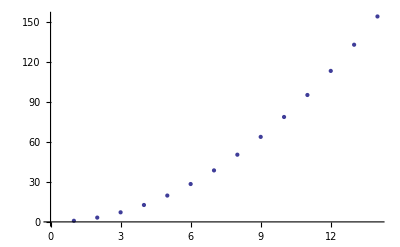

```mathematica
ErrorBarPlots`ErrorListPlot[final]
```

```mathematica
loglog=Table[{Log[2,N[i]],Log[2,final[[i,1]]]},{i,1,Length[final]}]
```

{{0.,-0.249318},{1.,1.69085},{1.58496,2.84413},{2.,3.66552},{2.32193,4.30547},{2.58496,4.82918},{2.80735,5.27241},{3.,5.65662},{3.16993,5.99568},{3.32193,6.29909},{3.45943,6.57364},{3.58496,6.82434},{3.70044,7.055},{3.80735,7.26859}}

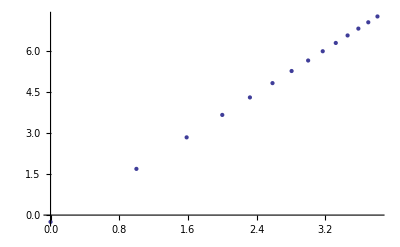

```mathematica
ListPlot[loglog]
```

```mathematica
fit=LinearModelFit[loglog,x,x]
```

FittedModel[-0.27899+1.97938 x]

```mathematica
fit["RSquared"]
```

0.99997

Linear wooooo!

```mathematica
f[x_] :=Normal[fit]
```

```mathematica
f[x]
```

-0.27899+1.97938 x

```mathematica
fit["ParameterErrors"]
```

{0.0088264,0.00314087}

```mathematica
Exp[-0.2789898192883946]
```

0.756548

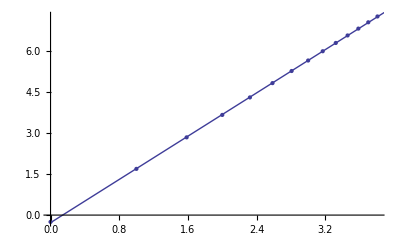

```mathematica
Show[ListPlot[loglog], Plot[f[x], {x, 0, 4}]]
```